## Skew-Takagi factorization

## Skew-Takagi factorization itself

### The algorithm

```mathematica
(* Skew-Takagi factorization *)
J[n_]:=If[EvenQ[n],KroneckerProduct[IdentityMatrix[n/2],({{0, 1}, {-1, 0}})],If[n==1,{{1}},ArrayFlatten[({{KroneckerProduct[IdentityMatrix[(n-1)/2],({{0, 1}, {-1, 0}})], 0}, {0, 1}})]]];
SkewTakagi[A_]:=Module[{U,Λ,V},
{U,Λ,V}=SingularValueDecomposition[A];
{Λ,U.MatrixPower[ConjugateTranspose[U].Conjugate[V].J[Length[A]],1/2]}

];
```

### Tesing the algorithm

```mathematica
(* The function generating a random skew-symmetric matrix *)
RandomSkewSym[n_]:=(# - Transpose[#])&@RandomComplex[{-1-ⅈ,1+ⅈ},{n,n}];
(* Single-run testing *)
Module[{n,U,Λ,A},
n=10;
A=RandomSkewSym[n];
{Λ,U}=SkewTakagi[A];
Print["Skewsymmetric: ",AntisymmetricMatrixQ[A]];
Print["Unitarity: ",UnitaryMatrixQ[U]];
Print["Diagonality: ",DiagonalMatrixQ[Λ]];
Print["Aquarcy of skew-Takagi: ",Norm[A-U.Λ.J[n].Transpose[U],"Frobenius"]];
]
```

Skewsymmetric: True

Unitarity: True

Diagonality: True

Aquarcy of skew-Takagi: 3.14518×10^-14

#### Timing

```mathematica
Monitor[timingList=Table[{i,Timing[SkewTakagi[RandomSkewSym[i]];][[1]]},{i,500,2000,100}],i]
```

{{500,0.96875},{600,1.6875},{700,2.34375},{800,3.4375},{900,5.04688},{1000,6.35938},{1100,8.4375},{1200,10.7969},{1300,13.7969},{1400,16.5781},{1500,19.5625},{1600,23.7656},{1700,28.8281},{1800,34.25},{1900,39.625},{2000,46.0781}}

Fit for CPU time cost

```mathematica
timingFit=Exp[Fit[Log[N@timingList],{1,y},y]/.y->Log[n]]
```

3.10071×10^-8 n^2.77527

Plot for CPU time cost (both data and fit)

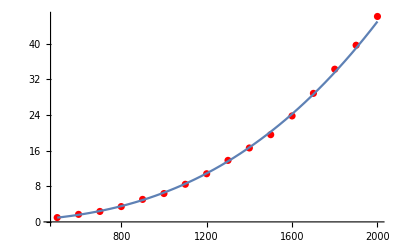

```mathematica
Show[ListPlot[timingList, PlotStyle->Red],Plot[timingFit,{n,500, 2000}]]
```

#### Computational error

```mathematica
RandomErrorTest[n_]:=
Module[{U,Λ,A},
A=RandomSkewSym[n];
{Λ,U}=SkewTakagi[A];

Norm[A-U.Λ.J[n].Transpose[U],"Frobenius"]
];
Monitor[errorList=Table[{i,RandomErrorTest[i]},{i,500,2000,100}],i]
```

{{500,2.66841×10^-11},{600,2.8109×10^-11},{700,2.03216×10^-11},{800,5.28795×10^-11},{900,2.77755×10^-11},{1000,3.59112×10^-11},{1100,7.21438×10^-11},{1200,4.66322×10^-11},{1300,6.6773×10^-11},{1400,6.64867×10^-11},{1500,1.05205×10^-10},{1600,1.26227×10^-10},{1700,6.60892×10^-11},{1800,8.34839×10^-11},{1900,8.45841×10^-11},{2000,9.65809×10^-11}}

Fit for error (in sense of Frobenius norm)

```mathematica
errorFit=Exp[Fit[Log[N@errorList],{1,y},y]/.y->Log[n]]
```

2.04715×10^-14 n^1.11983

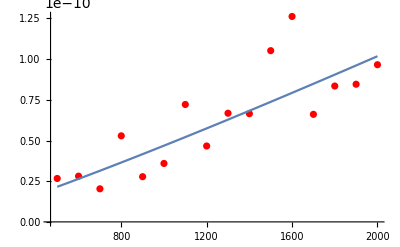

```mathematica
Show[ListPlot[errorList, PlotStyle->Red],Plot[errorFit,{n,500,2000}]]
```

## Application to quadratic Hamiltonians

Implementation of fermionic creation  - annihilation operators and quadratic Hamiltonians

```mathematica
σ3=({{1, 0}, {0, -1}});σp=({{0, 1}, {0, 0}});σm=({{0, 0}, {1, 0}});
fun1[k_]/;(k≥2):=Nest[KroneckerProduct[σ3,#]&,σ3,k-2];
fun1[1]={{1}};
cm[n_,k_]:=Fold[KroneckerProduct,fun1[k],{σm,IdentityMatrix[2^(n-k)]}];
cp[n_,k_]:=Fold[KroneckerProduct,fun1[k],{σp,IdentityMatrix[2^(n-k)]}];
Ham[A_]:=Sum[ⅈ/2(A[[i,j]] cp[Length[A],i].cp[Length[A],j]+Conjugate[A[[i,j]]] cm[Length[A],i].cm[Length[A],j]),{i,1,Length[A]},{j,1,Length[A]}];
```

Algorithms for Heisenberg evolution based on skew-Takagi factorization and on direct computaion of matrix exponential

```mathematica
CtHeisenberg[A_,t_]:=Table[MatrixExp[ⅈ Ham[A]t].cm[Length[A],i].MatrixExp[-ⅈ Ham[A]t],{i,1,Length[A]}];
SkewTakagiBasedCtHeisenberg[A_,t_]:=Module[{n,Λ, U},
{Λ, U}=SkewTakagi[A];
n=Length[A];Table[∑_(j=1)^n (U.MatrixFunction[Cos,Λ t].ConjugateTranspose[U])[[i,j]]cm[n,j]+ ∑_(j=1)^n (U.MatrixFunction[Sin,Λ t].J[n].Transpose[U])[[i,j]]cp[n,j],{i,1,n}]
]
```

#### Test that both methods coinside

```mathematica
Module[{n,t,A},
n=4;
t=1;
A=RandomSkewSym[n];
Norm[#,"Frobenius"]&/@(CtHeisenberg[A,t]-SkewTakagiBasedCtHeisenberg[A,t])
]
```

{2.87366×10^-15,2.97554×10^-15,3.73122×10^-15,4.18389×10^-15}

### Timing comparison

```mathematica
TimingComparison[n_]:=Module[{t,A},
t=1;
A=RandomSkewSym[n];
{n,Timing[CtHeisenberg[A,t];][[1]],Timing[SkewTakagiBasedCtHeisenberg[A,t];][[1]]}
];
Monitor[timingComparisonData=Table[TimingComparison[n],{n,1,10}],n]
```

{{1,0.,0.},{2,0.,0.},{3,0.,0.},{4,0.015625,0.},{5,0.078125,0.015625},{6,0.34375,0.015625},{7,1.60938,0.078125},{8,8.45313,0.265625},{9,53.9375,1.15625},{10,432.703,5.95313}}

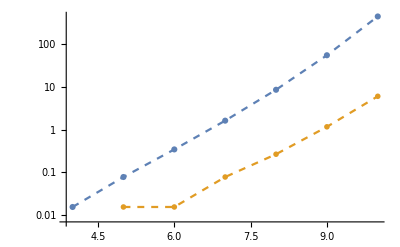

```mathematica
ListLogPlot[{{#[[1]],#[[2]]}&/@timingComparisonData,{#[[1]],#[[3]]}&/@timingComparisonData},PlotRange->All, Joined->True, PlotMarkers->{Automatic,"OpenMarkers"},PlotStyle->{Dashed}]
```